```mathematica
ToConjunction2[assigns_]:=Block[{exp=assigns[[1]]},
Table[exp=exp&& val,{val,Rest[assigns]}];
exp
]
```

```mathematica
NotFourForOuter[g_]:=ToConjunction2[Map[Symbol["x"<>ToString[#]]≠4&, Select[VertexList[g],#>5&]]]
```

```mathematica
GoodValue[n_,p_]:=Block[{vals=PadLeft[IntegerDigits[n,p],5]},vals[[2]]≥1&&vals[[3]]≥1&&vals[[4]]≥1&&vals[[5]]≥1]
```

```mathematica
SymbolToInt[x_]:=FromDigits[StringDrop[SymbolName[x],1]]
```

```mathematica
RemoveLowValues[assigns_]:=Select[assigns,SymbolToInt[#[[1]]]>5&]
```

```mathematica
ToConjunction[assigns_]:=Block[{exp=assigns[[1,1]]==assigns[[1,2]]},
Table[exp=exp&& val[[1]]==val[[2]],{val,Rest[assigns]}];
exp
]
```

```mathematica
PaintSolutions[record_]:=Block[{graphParm=PadLeft[IntegerDigits[record[[1]],record[[2]]],5], nonsols=record[[3]],g, constraints},
g=Graph[MakeInnerOuterGraph[graphParm]];

constraints=Map[ToConjunction[RemoveLowValues[#]]&&(((x2==x4)||(x2==x5))
||((x3==x5)||(x3==x1))
||((x4==x1)||(x4==x2))
||((x5==x2)||(x5==x3))
||((x1==x3)||(x1==x4)))&,nonsols]
;
Table[
PaintGraph3[g,cons, GraphLayout->"TutteEmbedding",VertexLabels->"Name"],
{cons,constraints}
]
]
```

```mathematica
HandleSolutions[record_]:=Block[{graphParm=PadLeft[IntegerDigits[record[[1]],record[[2]]],5], nonsols=record[[3]],g, constraints},
g=Graph[MakeInnerOuterGraph[graphParm]];
Print[g];
constraints=Map[ToConjunction[RemoveLowValues[#]]&,nonsols];
Monitor[
record[[1]]->
Table[
With[{curr=constraints[[k]]},
With[{result=
Table[
GraphSolutions3[g, h&& curr]
,{h,{True,((x1==x3)&&(x2==x4)),
((x2==x4)&&(x3==x5)),
((x3==x5)&&(x4==x1)),
((x4==x1)&&(x5==x2)),
((x5==x2)&&(x1==x3))}}
]},
If[Rest[result]=={0,0,0,0,0},Print[record[[1]]->curr ]];
Print[curr];
result
]],
{k,1,Length[constraints]}
],
{
record[[1]],h,k,Length[constraints]}
]
]
```

```mathematica
solutions2=With[
{pow=2},
Monitor[
Table[
With[
{g=VertexContract[VertexContract[Graph[MakeInnerOuterGraph[PadLeft[IntegerDigits[k,pow],5]]],{1,3}],{2,5}]},
{k,3,Join[ToVarsLogical [g,x6==1&&x7==2&&x8==1&&NotFourForOuter[g]],ToVarsLogical [g,x6==1&&x7==2&&x8==3&&NotFourForOuter[g]]]}]
,{k,Select[Range[0,pow^5-1],GoodValue[#,pow]&]}
],
{k,pow^5-1}
]
];Export["d:\\solutions2.m",solutions2]
```

d:\solutions2.m

```mathematica
solutions2=Get["d:\\solutions2.m"]
```

{{15,3,{{x4→1,x6→1,x7→2,x8→1,x9→2,x10→1,x11→2,x12→3,x13→2,x14→3,x1→3,x2→4},{x4→2,x6→1,x7→2,x8→1,x9→2,x10→3,x11→1,x12→3,x13→1,x14→2,x1→4,x2→3},{x4→1,x6→1,x7→2,x8→3,x9→2,x10→1,x11→2,x12→3,x13→2,x14→3,x1→3,x2→4},{x4→2,x6→1,x7→2,x8→3,x9→1,x10→2,x11→1,x12→3,x13→1,x14→2,x1→3,x2→4},{x4→2,x6→1,x7→2,x8→3,x9→1,x10→2,x11→1,x12→3,x13→1,x14→3,x1→3,x2→4}}},{31,3,{{x4→1,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→3,x14→2,x15→3,x1→3,x2→4},{x4→2,x6→1,x7→2,x8→1,x9→2,x10→1,x11→2,x12→1,x13→3,x14→1,x15→2,x1→3,x2→4},{x4→2,x6→1,x7→2,x8→1,x9→2,x10→1,x11→2,x12→1,x13→3,x14→1,x15→2,x1→4,x2→3},{x4→2,x6→1,x7→2,x8→1,x9→2,x10→1,x11→2,x12→1,x13→3,x14→1,x15→3,x1→3,x2→4},{x4→2,x6→1,x7→2,x8→1,x9→2,x10→1,x11→3,x12→1,x13→3,x14→1,x15→2,x1→4,x2→3},{x4→2,x6→1,x7→2,x8→1,x9→3,x10→1,x11→2,x12→1,x13→3,x14→1,x15→2,x1→3,x2→4},{x4→2,x6→1,x7→2,x8→1,x9→3,x10→1,x11→2,x12→1,x13→3,x14→1,x15→3,x1→3,x2→4},{x4→3,x6→1,x7→2,x8→1,x9→3,x10→1,x11→2,x12→1,x13→2,x14→1,x15→3,x1→4,x2→2},{x4→3,x6→1,x7→2,x8→1,x9→3,x10→1,x11→3,x12→1,x13→2,x14→1,x15→3,x1→4,x2→2},{x4→4,x6→1,x7→2,x8→1,x9→3,x10→1,x11→2,x12→1,x13→2,x14→1,x15→3,x1→3,x2→2},{x4→4,x6→1,x7→2,x8→1,x9→3,x10→1,x11→2,x12→1,x13→3,x14→1,x15→3,x1→3,x2→2},{x4→3,x6→1,x7→2,x8→3,x9→1,x10→3,x11→2,x12→1,x13→2,x14→1,x15→3,x1→4,x2→2}}}}

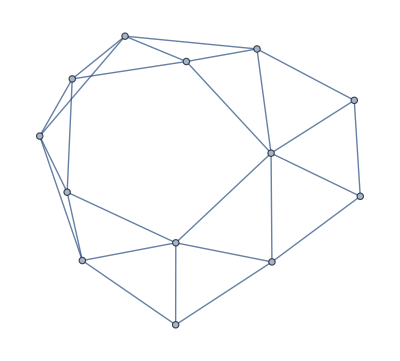

x6==1&&x7==2&&x8==1&&x9==2&&x10==1&&x11==2&&x12==3&&x13==2&&x14==3

x6==1&&x7==2&&x8==1&&x9==2&&x10==3&&x11==1&&x12==3&&x13==1&&x14==2

x6==1&&x7==2&&x8==3&&x9==2&&x10==1&&x11==2&&x12==3&&x13==2&&x14==3

x6==1&&x7==2&&x8==3&&x9==1&&x10==2&&x11==1&&x12==3&&x13==1&&x14==2

x6==1&&x7==2&&x8==3&&x9==1&&x10==2&&x11==1&&x12==3&&x13==1&&x14==3

15→{{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}}}

```mathematica
Map[HandleSolutions[#]&,Take[solutions2,1]]//TableForm
```

```mathematica
VertexList[-Graphics-]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
PaintGraph3[-Graphics-,x6==1&&x7==2&&x8==1&&x9==2&&x10==1&&x11==2&&x12==3&&x13==2&&x14==3, GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

{}

```mathematica
.
```

```mathematica
IntegerDigits[15,2]
```

{1,1,1,1}

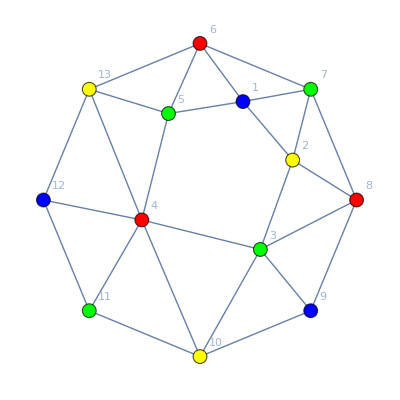
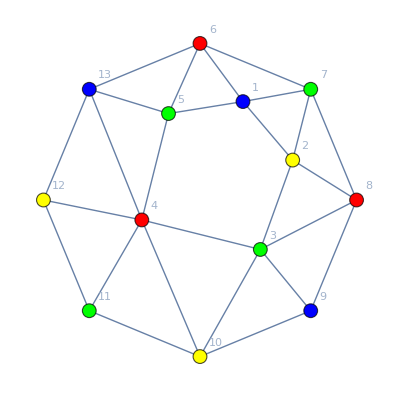
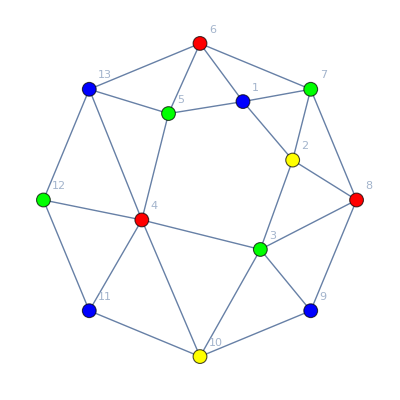
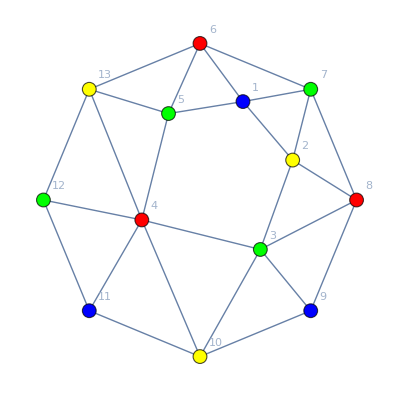
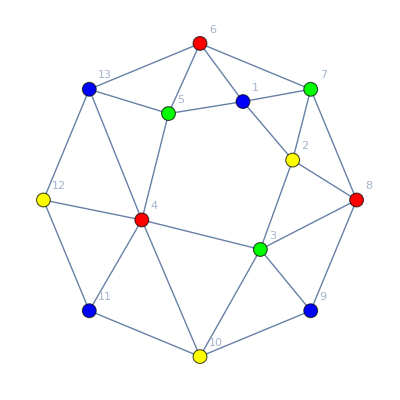
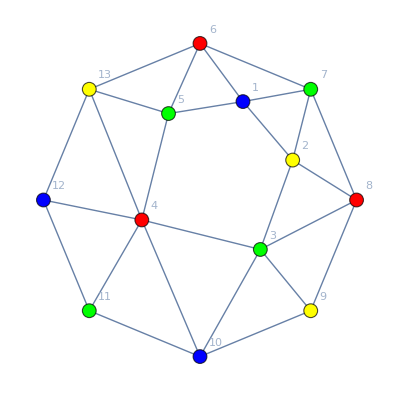
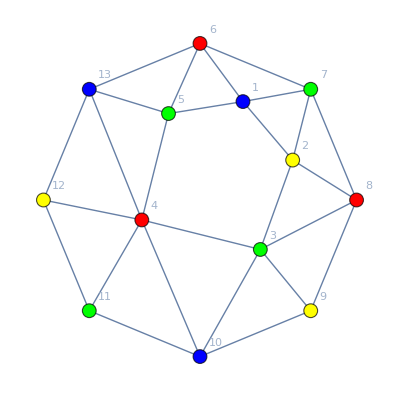
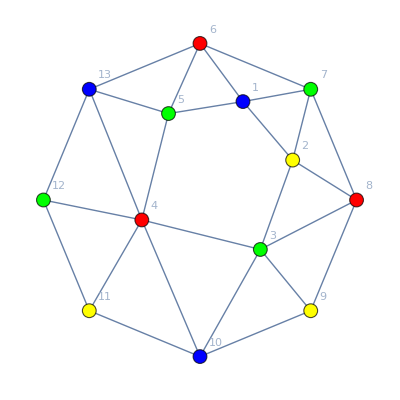
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PaintGraph3[Graph[MakeInnerOuterGraph[PadLeft[IntegerDigits[15,3],5]]],x6==1&&x7==2&&x8==1, GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```